# Regression Models for Real-value predictors

Regressions models are used for predicting real-valued outputs given a set of input features. Regression can be modelled as a function of a k-th degree polynomial of the input features.

When k=1, we have a regression model which assumes that the output is a linear function of the given input feature-set. Similarly, when k=2, we have a quadratic regression model and so on for increasing values of k.

The learning problem here is deriving the function, be it for any kth degree, of the inputs. This function is representated as a weight wector w. This vector consists of coefficients of the terms in the kth degree polynomial of input features we are trying to model. The derivation of w for linear regression given a training set consisting of input feature vectors Xi and corresponding outputs yi is:

X =(X_1
X_2
.
.
.
X_R)  = (x_11 | x_12 | . | . | . | x_(1m)
x_21 | x_22 | . | . | . | x_(2m)
. | . | . | . | . | .
. | . | . | . | . | .
. | . | . | . | . | .
x_R1 | x_R2 | . | . | . | x_Rm)              and                Y = (y_1
y_2
.
.
.
y_R)

The linear regression model assumes a vector w such that :

y = Out(x) = w^T. x = w_1x_1 + w_2x_2 + …. + w_mx_m

w = max. likelihood = (X^T X)^-1(X^T Y)

Z = (x_11 | x_12 | ... | x_(1m) | x_11^2 | x_12^2 | ... | (x_(1m))^2 | x_11 x_12 | x_11 x_13 | ...
x_21 | x_22 | ... | x_(2m) | x_11^2 | x_12^2 | ... | (x_(2m))^2 | x_21 x_22 | x_21 x_23 | ...
. | . | ... | . | . | . | ... | . | . | . | .
. | . | ... | . | . | . | ... | . | . | . | .
. | . | ... | . | . | . | ... | . | . | . | .
x_R1 | x_R2 | ... | x_Rm | x_R1^2 | x_R2^2 | ... | x_Rm^2 | x_R1 x_R2 | x_R1 x_R3 | ...)              and                Y = (y_1
y_2
.
.
.
y_R)

i.e. Z = {all products of powers of inputs in which sum of powers is q or less}

w is calculated as show above by replacing X with Z.

Through this tutorial we attempt to show :

1. How the w changes with increasing k

2. We plot a k^th-degree curve in x for each weight vector component w_i, with w_i as the constant coefficient for the curve. When predicting the output, the regression model will consider all vectors that are tangent to each of these curves (plotted using w_i) at the corresponding input values x_i, aggregate them into one vector and the magnitude of this vector is the predicted value for y.

3. We further show the change in mean error on a validation data set as k changes.

4. We have also provided a linear regression model with a threshold-value w_0 incorporated. This threshold aids as a counter to noise which may be present in the data. We show how the orientation of the vectors as well as the mean error changes due to this addition of w_0.

5. Lastly, beyond a certain k-value the model exhibits overfitting. i.e. it tries to fit the trainind data so much that it’s accuracy over unseen (test) data deteriorates. This phenomenon is show in the k=4 model at the end of this tutorial. The mean error for this model can be seen to have spiked up substantially providing evidence of this behavior.

Linear Multivariate Regression

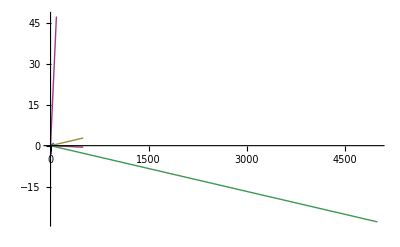

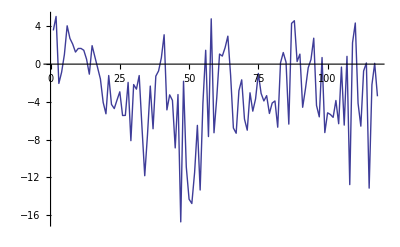

Mean Error →2.95038

```mathematica
Multivariate Linear Regression

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
testSetLength = 274;

X = autoMPGDataSet[[1;;testSetLength,2;;7]];
Y=autoMPGDataSet[[1;; testSetLength,1]];

β = Inverse[Transpose[X] . X ]  . (Transpose[X] . Y);

predictedSeperator1 = Table[β[[1]]*featureValue,{featureValue,12}];
predictedSeperator2 = Table[β[[2]]*featureValue,{featureValue,500}];
predictedSeperator3 = Table[β[[3]]*featureValue,{featureValue,500}];
predictedSeperator4 = Table[β[[4]]*featureValue,{featureValue,5000}];
predictedSeperator5 = Table[β[[5]]*featureValue,{featureValue,50}];
predictedSeperator6 = Table[β[[6]]*featureValue,{featureValue,90}];

predictedMPG = Table[β  . autoMPGDataSet[[i,2;;7]],{i,testSetLength+1,Length[autoMPGDataSet]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-actualMPG[[i]],{i,1,Length[predictedMPG]}];

ListLinePlot[{predictedSeperator1,predictedSeperator2,predictedSeperator3,predictedSeperator4,predictedSeperator5,predictedSeperator6}]
ListLinePlot[error]
"Mean Error "  -> Abs[Mean[error]]
```

### Multivariate Linear Regression w/ Threshold (w0)

{9.66918,-0.321159,-0.00100825,-0.00362564,-0.00531775,-0.0467459,0.415832}

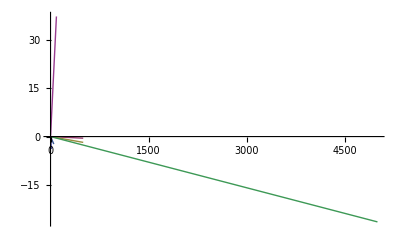

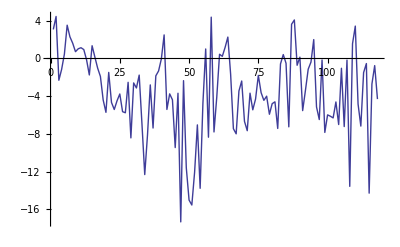

Mean Error →-3.57002

```mathematica
autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];

testSetLength = 274;

X = autoMPGDataSet[[1;;Length[autoMPGDataSet],2;;7]];
unaryRow=Table[1,{Length[autoMPGDataSet]}];
X = Insert[X//Transpose,unaryRow,1]//Transpose;
testX=X[[testSetLength+1;;Length[autoMPGDataSet],All]];
X=X[[1;;testSetLength,All]];

Y=autoMPGDataSet[[1;; testSetLength,1]];

β = Inverse[Transpose[X] . X ]  . (Transpose[X] . Y)

predictedMPG = Table[β  . X[[i,All]],{i,Length[X]}];

predictedSeperator1 = Table[β[[2]]*featureValue,{featureValue,12}];
predictedSeperator2 = Table[β[[3]]*featureValue,{featureValue,500}];
predictedSeperator3 = Table[β[[4]]*featureValue,{featureValue,500}];
predictedSeperator4 = Table[β[[5]]*featureValue,{featureValue,5000}];
predictedSeperator5 = Table[β[[6]]*featureValue,{featureValue,50}];
predictedSeperator6 = Table[β[[7]]*featureValue,{featureValue,90}];
ListLinePlot[{predictedSeperator1,predictedSeperator2,predictedSeperator3,predictedSeperator4,predictedSeperator5,predictedSeperator6}]


predictedMPG = Table[β  . testX[[i,All]],{i,1,Length[testX]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-actualMPG[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  -> Abs[Mean[error]]
```

### Multivariate Quadratic regression

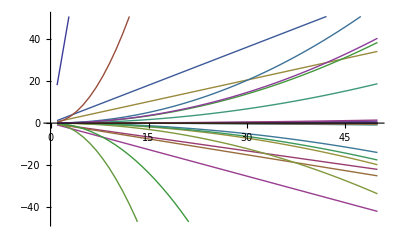

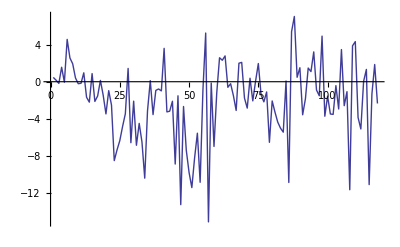

Mean Error →-2.0725

```mathematica
Off[Inverse::luc]

Multisets[l_List,k_]:=Union[Sort/@Flatten[Outer[List,Sequence@@Table[l,{k}]],k-1]]
Multisets[n_,k_]:=Multisets[Range[n],k]

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
testSetLength = 274;

listCombo = {};

For[i=1,i≤2,i++,listCombo = Union[listCombo,Multisets[{2,3,4,5,6,7},i]]];

newX = {};
For[vectorComponent=1,vectorComponent≤ Length[listCombo],vectorComponent++,
componentRow = Table[
Product[
autoMPGDataSet[[instance,listCombo[[vectorComponent,i]]]],
{i,1,Length[listCombo[[vectorComponent]]]}],
{instance,1,Length[autoMPGDataSet]}];
newX = Append[newX,componentRow];
]
newX = newX //Transpose;
testX = newX[[testSetLength+1;;Length[autoMPGDataSet],All]] ;
newX = newX[[1;;testSetLength,All]];

Y=autoMPGDataSet[[1;; testSetLength,1]];

β = Inverse[Transpose[newX] . newX ]  . (Transpose[newX] . Y);


vectorsInPredictor =  Table[
Table[
β[[vectorComponent]]*featureValue^Floor[ Log[8,vectorComponent]+1],
{featureValue,1,50}],
{vectorComponent,1,Length[β]}];


ListLinePlot[vectorsInPredictor]

predictedMPGTraining = Table[β  . newX[[i,All]],{i,Length[newX]}];

predictedMPG = Table[β  . testX[[i,All]],{i,1,Length[testX]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-actualMPG[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  ->Abs[ Mean[error]]
```

### Multivariate 3rd Degree Polynomial Regression Model

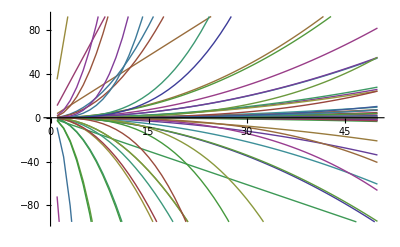

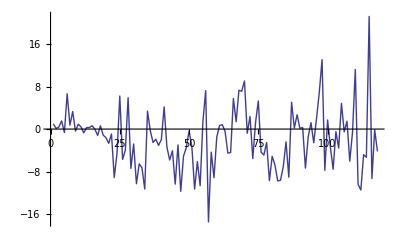

Mean Error →1.82174

```mathematica
Off[Inverse::luc]

Multisets[l_List,k_]:=Union[Sort/@Flatten[Outer[List,Sequence@@Table[l,{k}]],k-1]]
Multisets[n_,k_]:=Multisets[Range[n],k]

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
testSetLength = 274;

listCombo = {};

For[i=1,i≤3,i++,listCombo = Union[listCombo,Multisets[{2,3,4,5,6,7},i]]];

newX = {};
For[vectorComponent=1,vectorComponent≤ Length[listCombo],vectorComponent++,
componentRow = Table[
Product[
autoMPGDataSet[[instance,listCombo[[vectorComponent,i]]]],
{i,1,Length[listCombo[[vectorComponent]]]}],
{instance,1,Length[autoMPGDataSet]}];
newX = Append[newX,componentRow];
]
newX = newX //Transpose ;
testX = newX[[testSetLength+1;;Length[autoMPGDataSet],All]] ;
newX = newX[[1;;testSetLength,All]];
Y=autoMPGDataSet[[1;; testSetLength,1]];


β = Inverse[Transpose[newX] . newX ]  . (Transpose[newX] . Y);



vectorsInPredictor =  Table[
Table[
β[[vectorComponent]]*featureValue^Floor[ Log[8,vectorComponent]+1],
{featureValue,1,50}],
{vectorComponent,1,Length[β]}];


ListLinePlot[vectorsInPredictor]

predictedMPGTraining = Table[β  . newX[[i,All]],{i,Length[newX]}];

predictedMPG = Table[β  . testX[[i,All]],{i,1,Length[testX]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-actualMPG[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  -> Abs[Mean[error]]
```

### Multivariate 4th Degree Polynomial Regression Model

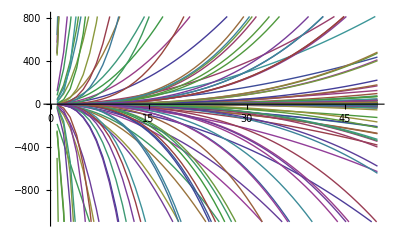

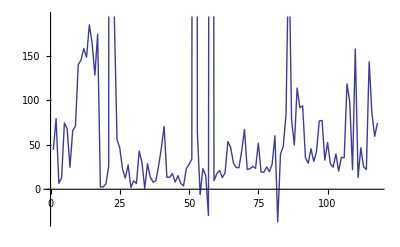

Mean Error →154.767

```mathematica
Off[Inverse::luc]

Multisets[l_List,k_]:=Union[Sort/@Flatten[Outer[List,Sequence@@Table[l,{k}]],k-1]]
Multisets[n_,k_]:=Multisets[Range[n],k]

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
testSetLength = 274;

listCombo = {};

For[i=1,i≤4,i++,listCombo = Union[listCombo,Multisets[{2,3,4,5,6,7},i]]];

newX = {};
For[vectorComponent=1,vectorComponent≤ Length[listCombo],vectorComponent++,
componentRow = Table[
Product[
autoMPGDataSet[[instance,listCombo[[vectorComponent,i]]]],
{i,1,Length[listCombo[[vectorComponent]]]}],
{instance,1,Length[autoMPGDataSet]}];
newX = Append[newX,componentRow];
]
newX = newX //Transpose ;
testX = newX[[testSetLength+1;;Length[autoMPGDataSet],All]] ;
newX = newX[[1;;testSetLength,All]];
Y=autoMPGDataSet[[1;; testSetLength,1]];


β = Inverse[Transpose[newX] . newX ]  . (Transpose[newX] . Y);



vectorsInPredictor =  Table[
Table[
β[[vectorComponent]]*featureValue^Floor[ Log[8,vectorComponent]+1],
{featureValue,1,50}],
{vectorComponent,1,Length[β]}];


ListLinePlot[vectorsInPredictor]

predictedMPGTraining = Table[β  . newX[[i,All]],{i,Length[newX]}];

predictedMPG = Table[β  . testX[[i,All]],{i,1,Length[testX]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-actualMPG[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  -> Abs[Mean[error]]
```